```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/LISA_Fisher/math

```mathematica
$Assumptions={A>0};
```

```mathematica
GWList=Import["dataIGWS_17012024/17012024gws_julia_csmin=1.000e-01_sigms=2.000e+00_rhoc=1.000e-08_deltacsmin=0.000e+00_deltasigma=0.000e+00.dat"];
GWListcsp=Import["dataIGWS_17012024/17012024gws_julia_csmin=1.100e-01_sigms=2.000e+00_rhoc=1.000e-08_deltacsmin=1.000e-02_deltasigma=0.000e+00.dat"];
GWListcsm=Import["dataIGWS_17012024/17012024gws_julia_csmin=9.000e-02_sigms=2.000e+00_rhoc=1.000e-08_deltacsmin=-1.000e-02_deltasigma=0.000e+00.dat"];
GWListsp=Import["dataIGWS_17012024/17012024gws_julia_csmin=1.000e-01_sigms=2.100e+00_rhoc=1.000e-08_deltacsmin=0.000e+00_deltasigma=1.000e-01.dat"];
GWListsm=Import["dataIGWS_17012024/17012024gws_julia_csmin=1.000e-01_sigms=1.900e+00_rhoc=1.000e-08_deltacsmin=0.000e+00_deltasigma=-1.000e-01.dat"];
```

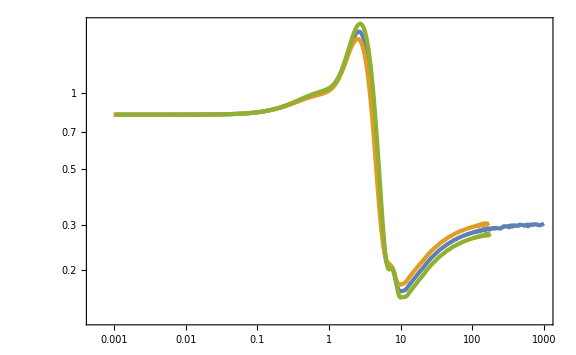

```mathematica
ListLogLogPlot[{GWList,GWListcsp,GWListcsm}]
```

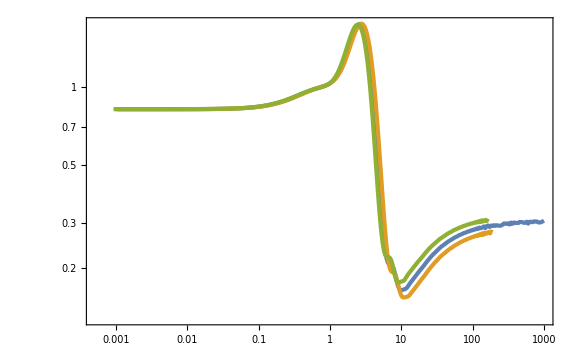

```mathematica
ListLogLogPlot[{GWList,GWListsp,GWListsm}]
```

```mathematica
dcs=0.01;
ds=0.1;
```

```mathematica
GWint[f_]=Interpolation[GWList][f];
GWintcsp[f_]=Interpolation[GWListcsp][f];
GWintcsm[f_]=Interpolation[GWListcsm][f];
GWintsp[f_]=Interpolation[GWListsp][f];
GWintsm[f_]=Interpolation[GWListsm][f];
```

```mathematica
dGWdcs[f_]=(GWintcsp[f]-GWintcsm[f])/(2dcs);
dGWds[f_]=(GWintsp[f]-GWintsm[f])/(2ds);
```

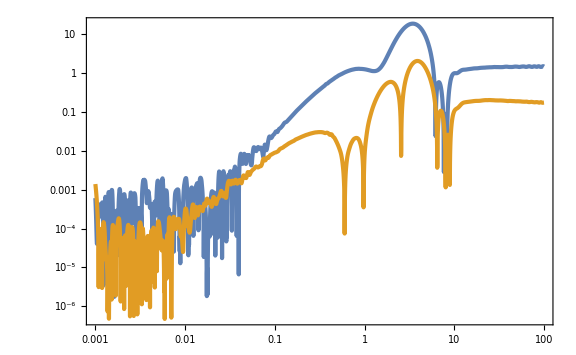

```mathematica
LogLogPlot[{Abs[dGWdcs[f]],Abs[dGWds[f]]},{f,10^-3,10^2}]
```

```mathematica
L=2.5 10^9(*m*);
Tobs=4 60 60 24 365(*s*)
fs=10^-3(*s^-1*);
Ωrh2=4.2 10^-5;
c=299792458(*m/s*);
pc=3.086 10^16(*m*);
Hnorm=(100 10^3)/(10^6 pc)(*s*)
fmax=10^2;
fmin=10^-3;
```

126144000

3.24044×10^-18

```mathematica
RAA[f_]=9/20 1/(1+0.7((2π f L)/c)^2);
REE[f_]=RAA[f];
RTT[f_]=9/20((2π f L)/c)^6/(1.8 10^3+0.7((2π f L)/c)^8);
```

```mathematica
calRAA[f_]=16 Sin[(2π f L)/c]^2((2π f L)/c)^2 RAA[f];
calREE[f_]=16 Sin[(2π f L)/c]^2((2π f L)/c)^2 REE[f];
calRTT[f_]=16 Sin[(2π f L)/c]^2((2π f L)/c)^2 RTT[f];
```

```mathematica
PIMS[f_]=P^2 10^(-12 2)(1+((2 10^-3)/f)^4)((2π f)/c)^2/.{P->15}(*s*);
Pacc[f_]=A^2 10^(-15 2)(1+((0.4 10^-3)/f)^2)(1+(f/(8 10^-3))^4)(1/(2π f))^4((2π f)/c)^2/.{A->3}(*s*);
```

```mathematica
NAA[f_]=8 Sin[(2π f L)/c]^2(4(1+Cos[(2π f L)/c]+Cos[(2π f L)/c]^2)Pacc[f]+(2+Cos[(2π f L)/c])PIMS[f]);
NEE[f_]=NAA[f];
NTT[f_]=16 Sin[(2π f L)/c]^2(1(1-Cos[(2π f L)/c])^2 Pacc[f]+(1-Cos[(2π f L)/c])PIMS[f]);
```

```mathematica
SnAA[f_]=NAA[f]/calRAA[f];
SnEE[f_]=NEE[f]/calREE[f];
SnTT[f_]=NTT[f]/calRTT[f];
```

```mathematica
ΩnAAh2[f_]=(4 π^2 f^3)/(3 Hnorm^2)SnAA[f];
ΩnEEh2[f_]=(4 π^2 f^3)/(3 Hnorm^2)SnEE[f];
ΩnTTh2[f_]=(4 π^2 f^3)/(3 Hnorm^2)SnTT[f];
```

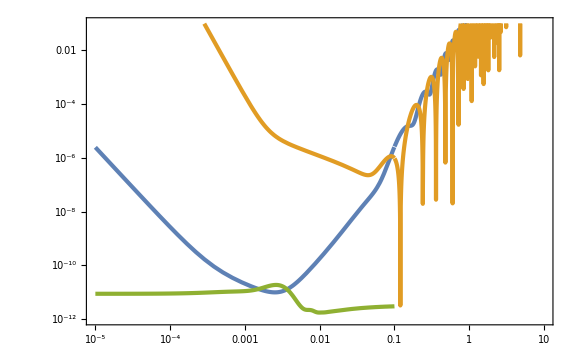

```mathematica
LogLogPlot[{ΩnAAh2[f],ΩnTTh2[f],GWint[f/fs]Ωrh2 (5 10^-4)^2 UnitStep[f/fs-fmin,fmax-f/fs]},{f,10^-5,10},PlotRange->{10^-12,10^-1}]
```

```mathematica
As=10^-5;
```

```mathematica
1/2 Tobs Ωrh2^2 As^4
```

1.11259×10^-21

```mathematica
(dGWds[f/fs]dGWds[f/fs])/((10^10 ΩnAAh2[f])^2)/.{f->0.003}
```

83.8306

```mathematica
NIntegrate[(dGWds[f/fs]dGWds[f/fs])/((10^10 ΩnAAh2[f])^2)+(dGWds[f/fs]dGWds[f/fs])/((10^10 ΩnEEh2[f])^2)+(dGWds[f/fs]dGWds[f/fs])/((10^10 ΩnTTh2[f])^2),{f,fs fmin,fs fmax}]
NIntegrate[E^lnf((dGWds[E^lnf/fs]dGWds[E^lnf/fs])/((10^10 ΩnAAh2[E^lnf])^2)+(dGWds[E^lnf/fs]dGWds[E^lnf/fs])/((10^10 ΩnEEh2[E^lnf])^2)+(dGWds[E^lnf/fs]dGWds[E^lnf/fs])/((10^10 ΩnTTh2[E^lnf])^2)),{lnf,Log[fs fmin],Log[fs fmax]}]
```

0.648986

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in lnf near {lnf} = {-5.51829}. NIntegrate obtained 0.648986 and 9.25421×10^-7 for the integral and error estimates.

0.648986

```mathematica
fs fmin
fs fmax
```

1/1000000

1/10

```mathematica
Fisher[A_]=0.11(A/As)^4{{NIntegrate[(dGWds[f/fs]dGWds[f/fs])/((10^10 ΩnAAh2[f])^2)+(dGWds[f/fs]dGWds[f/fs])/((10^10 ΩnEEh2[f])^2)+(dGWds[f/fs]dGWds[f/fs])/((10^10 ΩnTTh2[f])^2),{f,fs fmin,fs fmax}],NIntegrate[(dGWds[f/fs]dGWdcs[f/fs])/((10^10 ΩnAAh2[f])^2)+(dGWds[f/fs]dGWdcs[f/fs])/((10^10 ΩnEEh2[f])^2)+(dGWds[f/fs]dGWdcs[f/fs])/((10^10 ΩnTTh2[f])^2),{f,fs fmin,fs fmax}]},{NIntegrate[(dGWdcs[f/fs]dGWds[f/fs])/((10^10 ΩnAAh2[f])^2)+(dGWdcs[f/fs]dGWds[f/fs])/((10^10 ΩnEEh2[f])^2)+(dGWdcs[f/fs]dGWds[f/fs])/((10^10 ΩnTTh2[f])^2),{f,fs fmin,fs fmax}],NIntegrate[(dGWdcs[f/fs]dGWdcs[f/fs])/((10^10 ΩnAAh2[f])^2)+(dGWdcs[f/fs]dGWdcs[f/fs])/((10^10 ΩnEEh2[f])^2)+(dGWdcs[f/fs]dGWdcs[f/fs])/((10^10 ΩnTTh2[f])^2),{f,fs fmin,fs fmax}]}}
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in f near {f} = {0.00342667}. NIntegrate obtained -5.66897 and 0.000112894 for the integral and error estimates.

{{7.13885×10^18 A^4,-6.23586×10^19 A^4},{-6.23586×10^19 A^4,8.89939×10^20 A^4}}

```mathematica
CovC[A_]=Inverse[Fisher[A]]
```

{{(3.61097×10^-19)/A^4,(2.53023×10^-20)/A^4},{(2.53023×10^-20)/A^4,(2.89662×10^-21)/A^4}}

```mathematica
a[A_]=Sqrt[(CovC[A][[1,1]]+CovC[A][[2,2]])/2+Sqrt[(CovC[A][[1,1]]-CovC[A][[2,2]])^2/4+(CovC[A][[1,2]])^2]]//Simplify
b[A_]=Sqrt[(CovC[A][[1,1]]+CovC[A][[2,2]])/2-Sqrt[(CovC[A][[1,1]]-CovC[A][[2,2]])^2/4+(CovC[A][[1,2]])^2]]//Simplify
θ[A_]=ArcTan[(2CovC[A][[1,2]])/(CovC[A][[1,1]]-CovC[A][[2,2]])]/2//Simplify
```

(6.02392×10^-10)/A^2

(3.3439×10^-11)/A^2

0.0701729

```mathematica
α1=1.52;
α2=2.48;
```

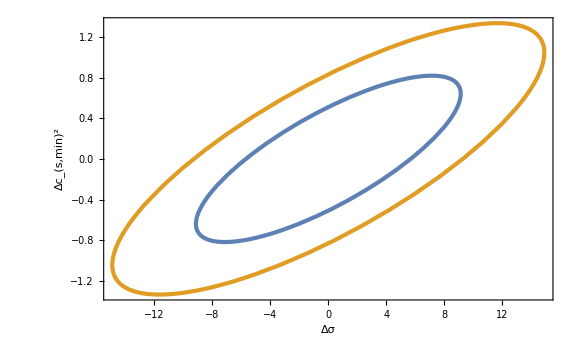

```mathematica
ParametricPlot[{α1 RotationMatrix[θ[As]].{a[As]Cos[t],b[As]Sin[t]},α2 RotationMatrix[θ[As]].{a[As]Cos[t],b[As]Sin[t]}},{t,0,2π},FrameLabel->{{Subscript[Δc, s,min]^2,None},{Δσ,Subscript[A, "s"]=="10^-5"}}]
```

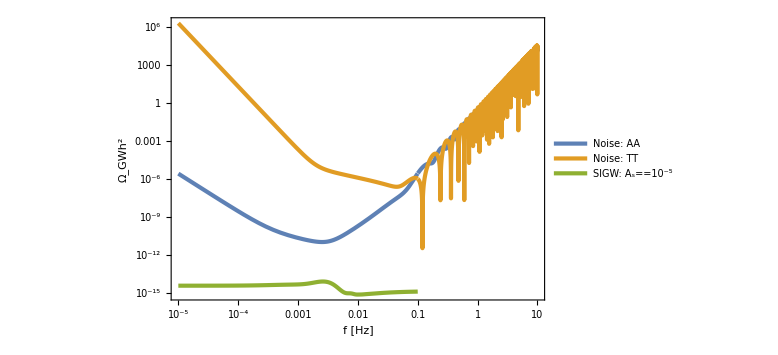

```mathematica
LogLogPlot[{ΩnAAh2[f],ΩnTTh2[f],GWint[f/fs]Ωrh2 As^2 UnitStep[f/fs-fmin,fmax-f/fs]},{f,10^-5,10},FrameLabel->{"f [Hz]","Ω_GWh^2"},PlotLegends->Placed[LineLegend[{"Noise: AA","Noise: TT",Row[{"SIGW: ",Subscript[A, "s"]=="10^-5"}]},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.55,0.8}]]
```